```mathematica
n=10;
a=1;
b=0.5;
c=10;
d=10;
```

```mathematica
A=SparseArray[{
Band[{2,1}]->(a+b),
Band[{1,1}]->-(2a+b),
Band[{1,2}]->a
},{n,n}];
A[[1,1]]=-(a+b);
A[[n,n]]=-a;
A=Normal[A];
MatrixForm[A];
```

```mathematica
(*s=Table[s[i],{i,1,n}]*)
s=Array[0&,n];
v=s;
v[[1]]=c-v[[1]];
v[[n]]=-d-v[[n]];
v
```

{10,0,0,0,0,0,0,0,0,-10}

```mathematica
ClearAll[Y,sol,system,init]
```

```mathematica
Ys[t_]:=Table[Y[i][t],{i,1,n}]
```

```mathematica
system=D[Ys[t],t]==A.Ys[t]+v;
Y0=Array[0&,n];
Y0[[1]]=10;
Y0[[n]]=100;
init=Ys[0]==Y0;
```

```mathematica
sol=NDSolveValue[{system,init},Ys[t],{t,0,500}];
```

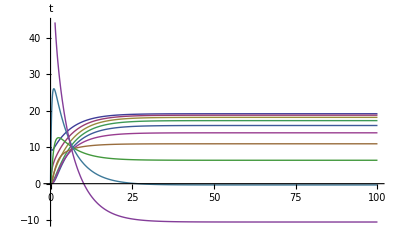

```mathematica
p=Plot[sol,{t,0,100},AxesLabel->{t,Automatic}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mrussell/phd/agent_based/gillespie

```mathematica
Export["plot.pdf",p]
```

plot.pdf